1.42+x

FittedModel[-4.80183+1.42216 x]

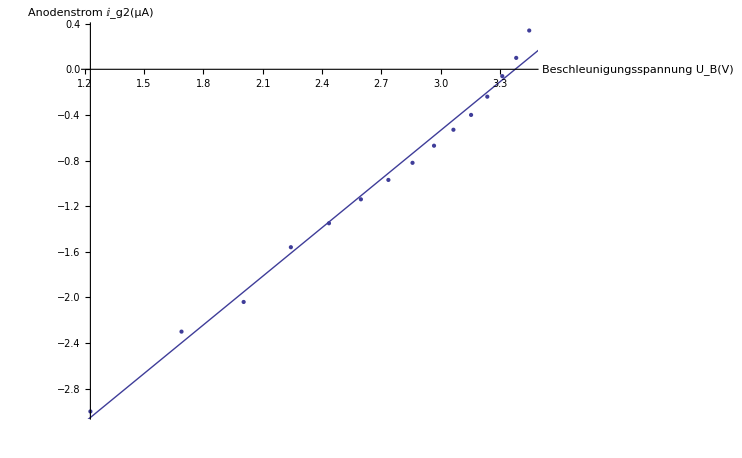

```mathematica
delta[x_]=x-1.98+3.4
data = {{Log[delta[2]], -3.00},{Log[delta[4]], -2.3},{Log[delta[6]], -2.04},{Log[delta[8]], -1.56},{Log[delta[10]], -1.35},{Log[delta[12]], -1.14},{Log[delta[14]], -0.97},{Log[delta[16]], -0.82}, {Log[delta[18]], -0.67}, {Log[delta[20]], -0.53}, {Log[delta[22]], -0.4}, {Log[delta[24]], -0.24}, {Log[delta[26]], -0.06}, {Log[delta[28]], 0.1}, {Log[delta[30]], 0.34}};
dplot = ListPlot[data];
model = LinearModelFit[data, x, x]
Show[dplot, Plot[model["BestFit"],{x, 0, 4}],AxesLabel->{Beschleunigungsspannung Subscript[U,B][V],Anodenstrom Subscript[I,g2] [μA]}]
```